## 《符号计算软件》 课程简介

本课程的教学目的是培养学生使用数学软件的能力。
课程主要介绍数学软件Mathematica的使用，以辅助大学基础课程和一些专业课程的教学。

教学形式：课堂教学+课后上机实践。

总评成绩：平时8次作业*50%+期末考试*50%。

平时作业为书后所有奇数号习题。

期末考试形式为开卷笔试。

## Mathematica简介

### 软件特点

Mathematica 是一个商业化的数学软件系统，由前端的用户交互界面、后端的系统内核、以及一套程序包组成。

Mathematica 使用其独有的 Wolfram 语言来从事程序设计和软件开发。

Mathematica 可以作为图形化的计算器使用，或者作为编程语言的GUI。

Mathematica 的程序及其运行结果可保存在同一个 nb 文档中，方便且直观。

Mathematica 具有丰富的免费资源，如帮助文档、演示项目、程序插件、数学知识库等。

相关链接

https://www.wolfram.com/mathematica/

https://www.wolfram.com/language/

https://www.wolfram.com/resources/

http://mathworld.wolfram.com/

### 一些例子

例：大整数运算

```mathematica
2^1000
```

```mathematica
1000!
```

例：π 的前 n 位

```mathematica
N[π,1000]
```

例：因式分解

```mathematica
FactorInteger[123456789101112131415161718192021222324252627282930]
```

```mathematica
Clear[x];Factor[x^255-1]
```

```mathematica
Clear[x];Factor[x^255-1,Modulus->2]
```

例：多项式展开

```mathematica
Clear[x,y];Expand[(x+y)^100]
```

例：最大公约数、 最小公倍数

```mathematica
GCD[123,456,789]
```

```mathematica
LCM[123,456,789]
```

```mathematica
PolynomialGCD[x^3+y^3,x^2-y^2]
```

```mathematica
PolynomialLCM[x^3+y^3,x^2-y^2]
```

例：数列求和

```mathematica
Sum[1/k^2, {k, 1, Infinity}]
```

例：方程求解

```mathematica
Solve[{3 x-2 y==5,x^2+y^2==5},{x,y}]
```

例：微积分

```mathematica
Clear[x];D[1/(1+x^2),x]
```

```mathematica
Clear[x];D[1/(1+x^2),{x,2}]
```

```mathematica
Clear[x];Integrate[1/(1+x^2),x]
```

例：矩阵运算

```mathematica
a={{1,2,3,4},{2,3,4,5},{3,4,5,6},{4,5,6,7}};a//MatrixForm
```

```mathematica
MatrixRank[a]
```

```mathematica
b=1/a;b//MatrixForm
```

```mathematica
Det[b]
```

```mathematica
Inverse[b]//MatrixForm
```

```mathematica
Eigenvalues[b]
```

```mathematica
N[%]
```

例：函数图像

```mathematica
Plot[Sin[x]/x,{x,-10,10}]
```

例 ：单叶双曲面 x^2/4+y^2/3-z^2/2=1

```mathematica
ContourPlot3D[x^2/4+y^2/3-z^2/2==1,{x,-10,10},{y,-10,10},{z,-5,5}]
```

```mathematica
ParametricPlot3D[Sqrt[1+z^2/2]{2Cos[t],Sqrt[3]Sin[t],0}+{0,0,z},{z,-5,5},{t,0,2Pi}]
```

例：Möbius带

```mathematica
r=5;k=5;
ParametricPlot3D[r{Cos[s],Sin[s],0}+t{Cos[s]Cos[k/2 s],Sin[s]Cos[k/2 s],Sin[k/2 s]},{s,0,2π},{t,-1,1},Axes->False,Boxed->False]
```

例：动画

```mathematica
(*圆摆线*)r1=10;r2=1;λ=-1;w=If[λ>0,r1+3r2,r1+r2];
Animate[Show[
Graphics[{Circle[{0,0},r1],Circle[{(r1+λ r2) Cos[s],(r1+λ r2) Sin[s]},r2],Line[{{(r1+λ r2)Cos[s],(r1+λ r2)Sin[s]},{(r1+λ r2)Cos[s]+r2 Cos[r1/r2 s],(r1+λ r2)Sin[s]+λ r2 Sin[r1/r2 s]}}]}],
ParametricPlot[{(r1+λ r2)Cos[t]+r2 Cos[r1/r2 t],(r1+λ r2)Sin[t]+λ r2 Sin[r1/r2 t]},{t,0,2Pi},PlotStyle->LightGray],PlotRange->{{-w,w},{-w,w}}
],{s,0,2 π}]
```

例：声音

```mathematica
Speak["University of Science and Technology of China"]
```

```mathematica
Sound[{SoundNote["G"],SoundNote["G"],SoundNote["G"],SoundNote["Eb",4]},1.5]
```

```mathematica
Sound[{SoundNote[-3,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-3,0.2],SoundNote[9,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,0.2],SoundNote[0,0.2],SoundNote[-1,0.2],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[4,2.4],SoundNote[2,0.2],SoundNote[0,0.2],SoundNote[-3,0.2],SoundNote[-5,0.2],SoundNote[-3,2.75],SoundNote[-3,0.8],SoundNote[-3,0.4],SoundNote[-1,0.2],SoundNote[0,1],SoundNote[None,0.25],SoundNote[-3,0.4],SoundNote[4,0.2],SoundNote[2,0.2],SoundNote[2,0.2],SoundNote[0,0.2],SoundNote[2,0.4],SoundNote[-3,0.2],SoundNote[2,1],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-1,0.2],SoundNote[-1,0.4],SoundNote[-3,0.4],SoundNote[-5,0.0],SoundNote[-5,0.6],SoundNote[-5,0.2],SoundNote[-5,0.4],SoundNote[-3,0],SoundNote[-1,0.4],SoundNote[0,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[-3,0.2],SoundNote[-3,0.4],SoundNote[-5,0.2],SoundNote[-3,1],SoundNote[None,0.3]}]
```

## 第1章 Mathematica的基本量

### 1.1 数字Number

联机帮助：Numbers

Mathematica中的数字一般为十进制的实数，可以是无误差的准确值，可以是带误差的小数值，也可以指定计算精度。

```mathematica
1/3
```

```mathematica
1.0/3
```

```mathematica
1.0``20/3
```

复数可以通过常数 I 实现。

```mathematica
I
```

```mathematica
(1+2 I)^2
```

常用的常数还有 π 和 E 等。

```mathematica
Pi
```

```mathematica
E
```

```mathematica
E^(Pi I)
```

出于计算效率的考虑，有时需要把准确值转化为小数值，或把小数值转化为准确值。

```mathematica
N[Pi,100]
```

```mathematica
n=1000000;Timing[a=(1+1/n)^n]
```

```mathematica
Timing[b=(1.0+1/n)^n]
```

```mathematica
Rationalize[b,0.1^20]
```

Mathematica也可以输入一个其他进制形式的数，或把一个数显示为其他进制形式。

```mathematica
2^^1110
```

```mathematica
16^^FFF0
```

```mathematica
BaseForm[2020,2]
```

注意：BaseForm的输出是一个对象，不是数/字符串/变元/列表，不能参与代数运算。

### 1.2 字符串String

联机帮助：Strings and Characters

字符串是双引号 “ ” 括起的一串字符。特殊字符的输入需要在字符前面加上 "\"。
注意中文字符与英文字符，全角字符与半角字符的不同。

```mathematica
s1="\"\\\""
StringLength[s1]
```

```mathematica
s2="中国科学技术大学"
StringLength[s2]
```

```mathematica
s3="USTC"
StringLength[s3]
```

```mathematica
Characters[s2]
```

```mathematica
s2<>" "<>s3
```

字符串与表达式的相互转换

```mathematica
ToExpression["Sin[Pi/3]"]
```

```mathematica
ToString[Sin[Pi/3]]
```

### 1.3 变元Symbol

联机帮助：Basic Objects

"变量的名称" 叫做变元。Mathematica的变量命名规则与常用编程语言大致相同，但也有其特点。

变元以字母开始，允许包含英文字母、希腊字母、汉字、数字、$ 等，区分大小写。

变元不允许包含运算符 !" # % &' ()*+, -. /:; <= > ?@[\]^`{|}~ 等。

变元不可以是数字、内置函数名、保留的关键词，如Sin, PI, E, I等。

注意区分"变量的名称"与"变量的取值"。

```mathematica
张3=1;李4=2;张3+李4
```

```mathematica
Clear[x];2+3x+x^2/.{2->3,3->4}
```

```mathematica
x=1;2+3x+x^2/.{2->3,3->4}
```

```mathematica
Clear[x];Sin'[x]
```

```mathematica
x=1;Sin'[x]
```

```mathematica
Clear[x];D[Sin[x],x]
```

```mathematica
x=1;D[Sin[x],x]
```

### 1.4 列表List

联机帮助：Lists

列表是大括号 { } 括起的一串表达式，可以用来表示集合、数列、向量等。

枚举输入一个列表

```mathematica
a={{1,2,3},{4,5,6}}
Grid[a,Frame->All]
MatrixForm[a]
TableForm[a]
```

注意：

Grid、MatrixForm、TableForm的输出是一个对象，不是数/字符串/变元/列表，不能参与代数运算。

从菜单项 "插入→表格/矩阵→新建" 得到的表格/矩阵是一个2维列表，可以参与代数运算。

```mathematica
a=({{1}, {2}, {3}})
```

{{1},{2},{3}}

```mathematica
Dimensions[a]
```

{3,1}

```mathematica
b=MatrixForm[a]
```

(1
2
3)

```mathematica
Dimensions[b]
```

{1}

```mathematica
c={1,2,3}
```

{1,2,3}

```mathematica
MatrixForm[c]
```

(1
2
3)

```mathematica
Dimensions[c]
```

{3}

通常使用Array或Table语句生成一个列表。

```mathematica
Clear[f,x];a=Array[f,{3,4}];b=Table[x[i]^(j-1),{i,3},{j,4}];{MatrixForm[a],MatrixForm[b]}
```

矩阵元素的提取和子矩阵的生成

```mathematica
a=Table[Subscript["a", i,j],{i,5},{j,5}];MatrixForm[a]
```

```mathematica
b=a⟦{1,2},{3,4,5}⟧;MatrixForm[b]
```

例：生成m行n列网格图的邻接矩阵。

```mathematica
{m,n}={3,4};a=Table[0,{m n},{m n}];Do[a[[(i-1)n+j,(i-1)n+j+1]]=1,{i,m},{j,n-1}];
Do[a[[(i-1)n+j,i n+j]]=1,{i,m-1},{j,n}];
a+=Transpose[a];MatrixForm[a]
```

(0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

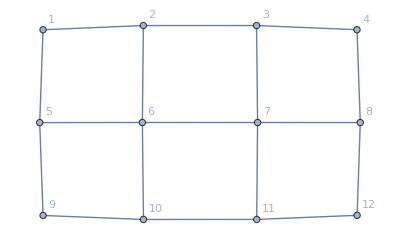

```mathematica
GraphPlot[a,VertexLabels->"Name"]
```

### 1.5 表达式Expression

联机帮助：Expressions

数字、字符串、变元是最基本的表达式。多个表达式通过运算符连接成复合表达式。所有Mathematica对象都可以认为是表达式。常见的表达式有：代数表达式、字符串表达式、逻辑表达式、关系型表达式（方程和不等式）、规则型表达式（函数、规则、模式）、图形对象等。

```mathematica
Roots[x^2==1,x]
```

```mathematica
Reduce[x^2≥1,x,Reals]
```

```mathematica
Solve[x^2==1,x]
```

表达式之间的转换

```mathematica
ToRules[x==-1||x==1]
```

```mathematica
s=ToString[Sqrt[1/2]]
```

```mathematica
Characters[s]
```

```mathematica
ToExpression["ArcSin[1/2]"]
```

定义函数的通常方式

```mathematica
Clear[f];f[x_]:=Cos[x];
```

```mathematica
x=0;y=Pi/2;{f[x],f[y]}
```

定义函数的错误方式

```mathematica
Clear[g,h];g[x]:=Cos[x];h[x_]=Cos[x];
```

```mathematica
t=Pi/6;{g[t],h[t]}
```

例 ：输入实数 b,c，输出方程 x^2+b x+c=0 的所有实根。

```mathematica
Clear[f];f[b_,c_]:=If[b^2<4 c,{},Union[{-b/2+√(b^2/4-c),-b/2-√(b^2/4-c)}]];
```

```mathematica
f[2,-1]
```